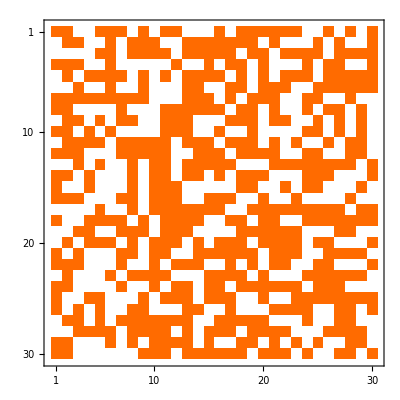

```mathematica
size=30;
p=0.58;
percolationDomain=Table[If[RandomReal[]<p,1,0],{x,1,size},{y,1,size}];
MatrixPlot[percolationDomain]
```

```mathematica
k=1;
reckognizedClusters=Table[0,{x,1,size},{y,1,size}];
Do[
If[percolationDomain[[x]][[y]]==1,reckognizedClusters[[x]][[y]]=k;k++];
,{x,1,size},{y,1,size}];
(reckognizedClusters)//MatrixForm
```

(1 | 2 | 0 | 0 | 3 | 4 | 5 | 0 | 6 | 0 | 7 | 8 | 0 | 0 | 0 | 9 | 0 | 10 | 11 | 12 | 13 | 14 | 15 | 0 | 0 | 16 | 0 | 17 | 0 | 18
0 | 19 | 20 | 0 | 0 | 21 | 0 | 22 | 23 | 24 | 0 | 0 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 0 | 32 | 0 | 0 | 0 | 33 | 0 | 34 | 0 | 0 | 35
0 | 0 | 0 | 0 | 36 | 37 | 0 | 38 | 39 | 40 | 41 | 0 | 42 | 43 | 44 | 45 | 46 | 0 | 47 | 48 | 0 | 49 | 50 | 51 | 52 | 0 | 53 | 54 | 55 | 56
57 | 58 | 59 | 0 | 0 | 60 | 0 | 0 | 0 | 0 | 0 | 61 | 0 | 0 | 62 | 0 | 63 | 64 | 0 | 65 | 0 | 0 | 0 | 66 | 0 | 67 | 68 | 0 | 0 | 69
0 | 70 | 0 | 71 | 72 | 73 | 74 | 0 | 75 | 0 | 76 | 0 | 77 | 78 | 79 | 80 | 0 | 81 | 0 | 82 | 0 | 83 | 84 | 85 | 0 | 86 | 87 | 88 | 89 | 90
0 | 0 | 91 | 0 | 0 | 92 | 0 | 0 | 93 | 0 | 0 | 0 | 94 | 95 | 0 | 0 | 96 | 97 | 0 | 98 | 99 | 100 | 0 | 0 | 101 | 102 | 103 | 104 | 105 | 106
107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 0 | 0 | 0 | 116 | 117 | 118 | 0 | 119 | 0 | 120 | 121 | 122 | 0 | 0 | 123 | 124 | 0 | 0 | 125 | 0 | 0
126 | 127 | 0 | 0 | 0 | 0 | 128 | 0 | 0 | 0 | 129 | 130 | 131 | 132 | 133 | 134 | 0 | 135 | 136 | 0 | 137 | 0 | 0 | 138 | 0 | 139 | 140 | 0 | 141 | 0
0 | 142 | 143 | 0 | 144 | 0 | 145 | 146 | 0 | 0 | 147 | 148 | 149 | 0 | 0 | 0 | 150 | 151 | 152 | 0 | 153 | 154 | 0 | 0 | 155 | 0 | 156 | 0 | 157 | 0
158 | 159 | 0 | 160 | 0 | 161 | 0 | 0 | 0 | 0 | 162 | 163 | 164 | 0 | 0 | 165 | 0 | 0 | 166 | 0 | 0 | 0 | 0 | 167 | 168 | 0 | 169 | 0 | 170 | 0
0 | 171 | 172 | 173 | 174 | 0 | 175 | 176 | 177 | 178 | 179 | 0 | 180 | 181 | 182 | 0 | 183 | 184 | 185 | 0 | 186 | 0 | 187 | 0 | 0 | 188 | 0 | 189 | 190 | 0
191 | 192 | 193 | 0 | 0 | 0 | 194 | 195 | 196 | 197 | 198 | 0 | 0 | 199 | 200 | 201 | 0 | 202 | 203 | 204 | 205 | 0 | 0 | 206 | 207 | 0 | 0 | 208 | 209 | 0
0 | 0 | 210 | 0 | 211 | 0 | 0 | 212 | 0 | 213 | 214 | 0 | 215 | 216 | 217 | 218 | 219 | 0 | 0 | 0 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 0 | 228
229 | 230 | 0 | 231 | 0 | 0 | 0 | 232 | 0 | 233 | 234 | 0 | 235 | 236 | 0 | 237 | 0 | 238 | 239 | 240 | 0 | 0 | 0 | 241 | 242 | 243 | 0 | 0 | 0 | 244
245 | 0 | 0 | 246 | 0 | 0 | 0 | 247 | 0 | 248 | 249 | 250 | 0 | 0 | 0 | 0 | 0 | 251 | 252 | 0 | 0 | 253 | 0 | 254 | 255 | 0 | 0 | 0 | 256 | 0
257 | 258 | 259 | 0 | 0 | 0 | 260 | 261 | 0 | 262 | 263 | 264 | 0 | 0 | 265 | 266 | 267 | 0 | 0 | 268 | 0 | 0 | 269 | 0 | 0 | 0 | 0 | 270 | 0 | 0
0 | 0 | 0 | 0 | 271 | 0 | 0 | 272 | 0 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 0 | 0 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 0 | 289 | 290
291 | 0 | 0 | 292 | 293 | 294 | 295 | 0 | 296 | 0 | 297 | 298 | 299 | 300 | 0 | 0 | 301 | 302 | 0 | 303 | 304 | 0 | 0 | 305 | 306 | 307 | 308 | 309 | 310 | 311
0 | 0 | 312 | 313 | 0 | 0 | 314 | 315 | 316 | 0 | 317 | 318 | 319 | 0 | 0 | 0 | 0 | 320 | 321 | 322 | 323 | 324 | 325 | 0 | 0 | 0 | 326 | 327 | 0 | 0
0 | 328 | 0 | 329 | 330 | 331 | 0 | 332 | 0 | 333 | 334 | 335 | 0 | 336 | 0 | 337 | 338 | 339 | 0 | 340 | 341 | 342 | 343 | 0 | 344 | 345 | 0 | 0 | 0 | 346
347 | 0 | 348 | 0 | 0 | 0 | 349 | 350 | 0 | 351 | 352 | 0 | 0 | 353 | 354 | 355 | 356 | 357 | 358 | 0 | 359 | 360 | 361 | 0 | 0 | 362 | 363 | 364 | 365 | 0
366 | 367 | 368 | 0 | 0 | 0 | 369 | 0 | 0 | 370 | 0 | 371 | 372 | 373 | 0 | 0 | 374 | 0 | 375 | 0 | 376 | 377 | 0 | 0 | 378 | 379 | 0 | 0 | 0 | 380
0 | 381 | 0 | 0 | 0 | 382 | 0 | 383 | 384 | 385 | 386 | 0 | 0 | 0 | 387 | 388 | 389 | 390 | 0 | 391 | 0 | 0 | 0 | 392 | 393 | 394 | 395 | 396 | 397 | 0
398 | 399 | 0 | 0 | 0 | 0 | 400 | 0 | 0 | 401 | 0 | 402 | 403 | 0 | 404 | 405 | 0 | 406 | 407 | 408 | 409 | 410 | 411 | 0 | 412 | 413 | 414 | 0 | 0 | 0
415 | 0 | 0 | 416 | 417 | 0 | 0 | 0 | 418 | 0 | 419 | 420 | 421 | 0 | 422 | 423 | 424 | 0 | 0 | 425 | 0 | 0 | 426 | 427 | 428 | 429 | 430 | 431 | 432 | 433
434 | 0 | 435 | 0 | 436 | 0 | 0 | 437 | 438 | 0 | 0 | 0 | 439 | 440 | 0 | 0 | 441 | 0 | 0 | 0 | 442 | 443 | 444 | 445 | 0 | 0 | 446 | 447 | 0 | 448
0 | 449 | 450 | 0 | 451 | 0 | 452 | 453 | 454 | 455 | 456 | 457 | 458 | 0 | 0 | 459 | 460 | 461 | 462 | 463 | 0 | 0 | 0 | 464 | 0 | 0 | 465 | 466 | 0 | 0
0 | 0 | 467 | 468 | 469 | 470 | 0 | 471 | 472 | 473 | 474 | 0 | 475 | 0 | 476 | 477 | 478 | 0 | 479 | 480 | 481 | 482 | 0 | 0 | 0 | 483 | 484 | 485 | 486 | 0
487 | 488 | 0 | 0 | 0 | 489 | 0 | 490 | 0 | 491 | 492 | 493 | 494 | 0 | 495 | 0 | 0 | 496 | 497 | 0 | 498 | 0 | 499 | 0 | 500 | 0 | 0 | 501 | 502 | 0
503 | 504 | 0 | 0 | 0 | 0 | 0 | 0 | 505 | 506 | 507 | 0 | 508 | 509 | 510 | 511 | 512 | 513 | 0 | 514 | 515 | 516 | 0 | 517 | 0 | 0 | 518 | 519 | 0 | 520)

```mathematica
Do[
Do[
If[percolationDomain[[x]][[y]]==1,
If[percolationDomain[[x-1]][[y]]==1,
Billy=Max[reckognizedClusters[[x]][[y]],reckognizedClusters[[x-1]][[y]]];
reckognizedClusters[[x]][[y]]=Billy;
reckognizedClusters[[x-1]][[y]]=Billy;
];
If[percolationDomain[[x]][[y-1]]==1,
Billy=Max[reckognizedClusters[[x]][[y]],reckognizedClusters[[x]][[y-1]]];
reckognizedClusters[[x]][[y]]=Billy;
reckognizedClusters[[x]][[y-1]]=Billy;
];
],

{x,2,size},{y,2,size}];,{iterations,1,66}]
(reckognizedClusters)//MatrixForm
```

(1 | 20 | 0 | 0 | 3 | 210 | 5 | 0 | 41 | 0 | 7 | 8 | 0 | 0 | 0 | 401 | 0 | 401 | 401 | 12 | 32 | 14 | 15 | 0 | 0 | 16 | 0 | 17 | 0 | 138
0 | 20 | 20 | 0 | 0 | 210 | 0 | 41 | 41 | 41 | 0 | 0 | 401 | 401 | 401 | 401 | 401 | 401 | 401 | 0 | 32 | 0 | 0 | 0 | 401 | 0 | 138 | 0 | 0 | 138
0 | 0 | 0 | 0 | 210 | 210 | 0 | 41 | 41 | 41 | 41 | 0 | 401 | 401 | 401 | 401 | 401 | 0 | 401 | 401 | 0 | 401 | 401 | 401 | 401 | 0 | 138 | 138 | 138 | 138
70 | 70 | 70 | 0 | 0 | 210 | 0 | 0 | 0 | 0 | 0 | 61 | 0 | 0 | 401 | 0 | 401 | 401 | 0 | 401 | 0 | 0 | 0 | 401 | 0 | 138 | 138 | 0 | 0 | 138
0 | 70 | 0 | 210 | 210 | 210 | 210 | 0 | 210 | 0 | 76 | 0 | 401 | 401 | 401 | 401 | 0 | 401 | 0 | 401 | 0 | 401 | 401 | 401 | 0 | 138 | 138 | 138 | 138 | 138
0 | 0 | 210 | 0 | 0 | 210 | 0 | 0 | 210 | 0 | 0 | 0 | 401 | 401 | 0 | 0 | 401 | 401 | 0 | 401 | 401 | 401 | 0 | 0 | 138 | 138 | 138 | 138 | 138 | 138
210 | 210 | 210 | 210 | 210 | 210 | 210 | 210 | 210 | 0 | 0 | 0 | 401 | 401 | 401 | 0 | 401 | 0 | 401 | 401 | 401 | 0 | 0 | 138 | 138 | 0 | 0 | 138 | 0 | 0
210 | 210 | 0 | 0 | 0 | 0 | 210 | 0 | 0 | 0 | 401 | 401 | 401 | 401 | 401 | 401 | 0 | 401 | 401 | 0 | 401 | 0 | 0 | 138 | 0 | 169 | 169 | 0 | 401 | 0
0 | 210 | 210 | 0 | 144 | 0 | 210 | 210 | 0 | 0 | 401 | 401 | 401 | 0 | 0 | 0 | 401 | 401 | 401 | 0 | 401 | 401 | 0 | 0 | 168 | 0 | 169 | 0 | 401 | 0
210 | 210 | 0 | 210 | 0 | 161 | 0 | 0 | 0 | 0 | 401 | 401 | 401 | 0 | 0 | 165 | 0 | 0 | 401 | 0 | 0 | 0 | 0 | 168 | 168 | 0 | 169 | 0 | 401 | 0
0 | 210 | 210 | 210 | 210 | 0 | 401 | 401 | 401 | 401 | 401 | 0 | 401 | 401 | 401 | 0 | 401 | 401 | 401 | 0 | 401 | 0 | 187 | 0 | 0 | 188 | 0 | 401 | 401 | 0
210 | 210 | 210 | 0 | 0 | 0 | 401 | 401 | 401 | 401 | 401 | 0 | 0 | 401 | 401 | 401 | 0 | 401 | 401 | 401 | 401 | 0 | 0 | 401 | 401 | 0 | 0 | 401 | 401 | 0
0 | 0 | 210 | 0 | 211 | 0 | 0 | 401 | 0 | 401 | 401 | 0 | 401 | 401 | 401 | 401 | 401 | 0 | 0 | 0 | 401 | 401 | 401 | 401 | 401 | 401 | 401 | 401 | 0 | 244
230 | 230 | 0 | 246 | 0 | 0 | 0 | 401 | 0 | 401 | 401 | 0 | 401 | 401 | 0 | 401 | 0 | 252 | 252 | 252 | 0 | 0 | 0 | 401 | 401 | 401 | 0 | 0 | 0 | 244
245 | 0 | 0 | 246 | 0 | 0 | 0 | 401 | 0 | 401 | 401 | 401 | 0 | 0 | 0 | 0 | 0 | 252 | 252 | 0 | 0 | 253 | 0 | 401 | 401 | 0 | 0 | 0 | 256 | 0
259 | 259 | 259 | 0 | 0 | 0 | 401 | 401 | 0 | 401 | 401 | 401 | 0 | 0 | 401 | 401 | 401 | 0 | 0 | 519 | 0 | 0 | 519 | 0 | 0 | 0 | 0 | 270 | 0 | 0
0 | 0 | 0 | 0 | 369 | 0 | 0 | 401 | 0 | 401 | 401 | 401 | 401 | 401 | 401 | 401 | 0 | 0 | 519 | 519 | 519 | 519 | 519 | 519 | 519 | 519 | 519 | 0 | 519 | 519
291 | 0 | 0 | 369 | 369 | 369 | 369 | 0 | 369 | 0 | 401 | 401 | 401 | 401 | 0 | 0 | 519 | 519 | 0 | 519 | 519 | 0 | 0 | 519 | 519 | 519 | 519 | 519 | 519 | 519
0 | 0 | 369 | 369 | 0 | 0 | 369 | 369 | 369 | 0 | 401 | 401 | 401 | 0 | 0 | 0 | 0 | 519 | 519 | 519 | 519 | 519 | 519 | 0 | 0 | 0 | 519 | 519 | 0 | 0
0 | 328 | 0 | 369 | 369 | 369 | 0 | 369 | 0 | 401 | 401 | 401 | 0 | 519 | 0 | 519 | 519 | 519 | 0 | 519 | 519 | 519 | 519 | 0 | 519 | 519 | 0 | 0 | 0 | 346
347 | 0 | 399 | 0 | 0 | 0 | 369 | 369 | 0 | 401 | 401 | 0 | 0 | 519 | 519 | 519 | 519 | 519 | 519 | 0 | 519 | 519 | 519 | 0 | 0 | 519 | 519 | 519 | 519 | 0
399 | 399 | 399 | 0 | 0 | 0 | 369 | 0 | 0 | 401 | 0 | 519 | 519 | 519 | 0 | 0 | 519 | 0 | 519 | 0 | 519 | 519 | 0 | 0 | 519 | 519 | 0 | 0 | 0 | 380
0 | 399 | 0 | 0 | 0 | 382 | 0 | 401 | 401 | 401 | 401 | 0 | 0 | 0 | 519 | 519 | 519 | 519 | 0 | 519 | 0 | 0 | 0 | 519 | 519 | 519 | 519 | 519 | 519 | 0
399 | 399 | 0 | 0 | 0 | 0 | 400 | 0 | 0 | 401 | 0 | 519 | 519 | 0 | 519 | 519 | 0 | 519 | 519 | 519 | 519 | 519 | 519 | 0 | 519 | 519 | 519 | 0 | 0 | 0
415 | 0 | 0 | 489 | 489 | 0 | 0 | 0 | 519 | 0 | 519 | 519 | 519 | 0 | 519 | 519 | 519 | 0 | 0 | 519 | 0 | 0 | 519 | 519 | 519 | 519 | 519 | 519 | 519 | 519
434 | 0 | 489 | 0 | 489 | 0 | 0 | 519 | 519 | 0 | 0 | 0 | 519 | 519 | 0 | 0 | 519 | 0 | 0 | 0 | 519 | 519 | 519 | 519 | 0 | 0 | 519 | 519 | 0 | 519
0 | 489 | 489 | 0 | 489 | 0 | 519 | 519 | 519 | 519 | 519 | 519 | 519 | 0 | 0 | 519 | 519 | 519 | 519 | 519 | 0 | 0 | 0 | 519 | 0 | 0 | 519 | 519 | 0 | 0
0 | 0 | 489 | 489 | 489 | 489 | 0 | 519 | 519 | 519 | 519 | 0 | 519 | 0 | 519 | 519 | 519 | 0 | 519 | 519 | 519 | 519 | 0 | 0 | 0 | 519 | 519 | 519 | 519 | 0
504 | 504 | 0 | 0 | 0 | 489 | 0 | 519 | 0 | 519 | 519 | 519 | 519 | 0 | 519 | 0 | 0 | 519 | 519 | 0 | 519 | 0 | 499 | 0 | 500 | 0 | 0 | 519 | 519 | 0
504 | 504 | 0 | 0 | 0 | 0 | 0 | 0 | 519 | 519 | 519 | 0 | 519 | 519 | 519 | 519 | 519 | 519 | 0 | 519 | 519 | 519 | 0 | 517 | 0 | 0 | 519 | 519 | 0 | 520)

```mathematica
Dynamic[p]
```

```mathematica
quantityOfClusters={};
sizeOfLargest={};
quantityOfFilledCells={};
sizeHistogram={};
```

```mathematica
For[p=0.1,p<0.9,p=p+0.025,
percolationDomain=Table[If[(RandomReal[]<p)&&1<x<size&&1<y<size,1,0],{x,1,size},{y,1,size}];
k=1;
reckognizedClusters=Table[0,{x,1,size},{y,1,size}];
Do[
If[percolationDomain[[x]][[y]]==1,reckognizedClusters[[x]][[y]]=k;k++];
,{x,1,size},{y,1,size}];

Do[

Do[
If[percolationDomain[[x]][[y]]==1,
If[percolationDomain[[x-1]][[y]]==1,
Billy=Max[reckognizedClusters[[x]][[y]],reckognizedClusters[[x-1]][[y]]];
reckognizedClusters[[x]][[y]]=Billy;
reckognizedClusters[[x-1]][[y]]=Billy;
];
If[percolationDomain[[x]][[y-1]]==1,
Billy=Max[reckognizedClusters[[x]][[y]],reckognizedClusters[[x]][[y-1]]];
reckognizedClusters[[x]][[y]]=Billy;
reckognizedClusters[[x]][[y-1]]=Billy;
];
If[percolationDomain[[x]][[y+1]]==1,
Billy=Max[reckognizedClusters[[x]][[y]],reckognizedClusters[[x]][[y+1]]];
reckognizedClusters[[x]][[y]]=Billy;
reckognizedClusters[[x]][[y+1]]=Billy;
];
If[percolationDomain[[x+1]][[y]]==1,
Billy=Max[reckognizedClusters[[x]][[y]],reckognizedClusters[[x+1]][[y]]];
reckognizedClusters[[x]][[y]]=Billy;
reckognizedClusters[[x+1]][[y]]=Billy;
];
],
{x,2,size-1},{y,2,size-1}];,{iterations,1,size^(3/2)}];
AppendTo[quantityOfFilledCells,{p,Total[percolationDomain,2]}];
AppendTo[quantityOfClusters,{p,CountDistinct[Flatten[reckognizedClusters]]}];
allSizes=Table[Count[Flatten[reckognizedClusters],clusterLable],{clusterLable,DeleteCases[DeleteDuplicates[Flatten[reckognizedClusters]],0]}];
AppendTo[sizeHistogram,{p,allSizes}];
AppendTo[sizeOfLargest,{p,Max[allSizes]}];
]
```

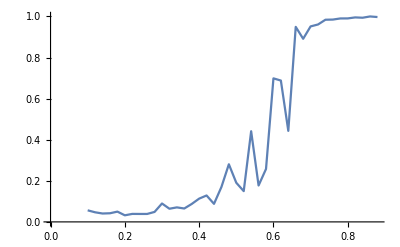

```mathematica
percolationFunction=Table[{sizeOfLargest[[i]][[1]],sizeOfLargest[[i]][[2]]/quantityOfFilledCells[[i]][[2]]},{i,1,Length[sizeOfLargest]}];ListPlot[percolationFunction,Joined->True]
```

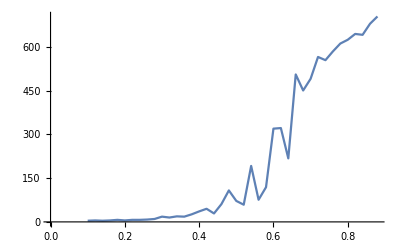

```mathematica
ListPlot[sizeOfLargest,Joined->True]
```

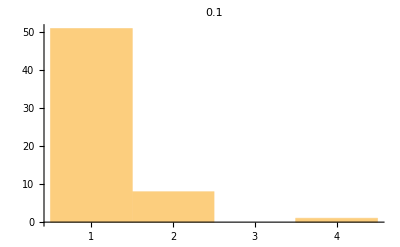

```mathematica
Histogram[sizeHistogram[[1]][[2]],20,PlotLabel->sizeHistogram[[1]][[1]]]
```

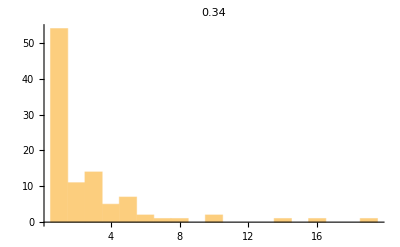

```mathematica
Histogram[sizeHistogram[[Round[Length[sizeHistogram]/3]]][[2]],20,PlotLabel->sizeHistogram[[Round[Length[sizeHistogram]/3]]][[1]]]
```

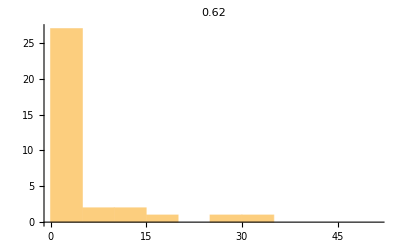

```mathematica
Histogram[sizeHistogram[[Round[2Length[sizeHistogram]/3]]][[2]],70,PlotLabel->sizeHistogram[[Round[2Length[sizeHistogram]/3]]][[1]]]
```